# Neural Networks

Use a GPU for training, when available:

```mathematica
SetOptions[NetTrain,TargetDevice->"GPU"];
```

### Balance Scale Example

```mathematica
net=NetGraph[{
CatenateLayer[],
DotPlusLayer[10],
ElementwiseLayer[Tanh],
DotPlusLayer[3],
SoftmaxLayer[]
},{
{NetPort["leftweight"],NetPort["leftdistance"],NetPort["rightweight"],NetPort["rightdistance"]}->1,
1->2->3->4->5->NetPort["balance"]
},
"leftweight"-> NetEncoder[{"Class",{1,2,3,4,5},"UnitVector"}],
"leftdistance"-> NetEncoder[{"Class",{1,2,3,4,5},"UnitVector"}],
"rightweight"-> NetEncoder[{"Class",{1,2,3,4,5},"UnitVector"}],
"rightdistance"-> NetEncoder[{"Class",{1,2,3,4,5},"UnitVector"}],
"balance"->NetDecoder[{"Class",{"L","B","R"}}]
]
```

NetGraph[]

```mathematica
rawdata=Import["http://archive.ics.uci.edu/ml/machine-learning-databases/balance-scale/balance-scale.data","CSV"];
```

```mathematica
training=Dataset[
Map[
AssociationThread[{"balance","leftweight","leftdistance","rightweight","rightdistance"}->#]&,
rawdata]
]
```

Dataset[<>]

```mathematica
result=NetTrain[net,training]
```

NetGraph[]

```mathematica
result[<|"leftweight"->1,"leftdistance"->1,"rightweight"->1,"rightdistance"->1|>]
```

B

```mathematica
result[<|"leftweight"->2,"leftdistance"->1,"rightweight"->1,"rightdistance"->1|>]
```

L

```mathematica
result[<|"leftweight"->2,"leftdistance"->1,"rightweight"->1,"rightdistance"->1|>]
```

L

```mathematica
test=Table[
{leftweight,leftdistance,rightweight,rightdistance}=RandomInteger[{1,5},4];
balance=rightweight*rightdistance-leftweight*leftdistance;
balance=Which[
balance<0,"L",
balance==0,"B",
balance>0,"R"
];
{leftweight,leftdistance,rightweight,rightdistance}->balance,
1000];
```

```mathematica
measurements=ClassifierMeasurements[result,test]
```

ClassifierMeasurementsObject[…]

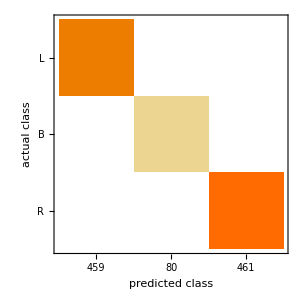

```mathematica
measurements["ConfusionMatrixPlot"]
```

### Car Evaluation Example

Source of the data set:

```mathematica
Hyperlink["http://archive.ics.uci.edu/ml/datasets/Car+Evaluation"]
```

Import the data as a .csv (comma separated file):

```mathematica
rawdata=Import["http://archive.ics.uci.edu/ml/machine-learning-databases/car/car.data","CSV"];
```

The number of rows in the data is 1728:

```mathematica
Length[rawdata]
```

1728

RandomSample lets you examine a few rows of data. Grid lets you format the data as a table. View a random sample of the data:

```mathematica
RandomSample[rawdata,10]//Grid[#,Frame->All,Alignment->Left]&
```

vhigh | vhigh | 4 | 4 | big | med | unacc
low | vhigh | 2 | more | big | low | unacc
med | low | 5more | 4 | small | high | good
high | med | 3 | more | small | low | unacc
vhigh | high | 5more | 2 | med | low | unacc
med | high | 5more | 2 | small | low | unacc
high | low | 3 | 2 | small | high | unacc
med | high | 2 | 4 | small | low | unacc
vhigh | low | 2 | 2 | med | med | unacc
med | vhigh | 3 | more | med | med | acc

Translate short abbreviated names to longer more descriptive names:

```mathematica
rawdata=rawdata/.{"vhigh"->"very high","med"->"medium","5more"->"5 or more","unacc"->"unacceptable","acc"->"acceptable","vgood"->"very good"};
```

```mathematica
RandomSample[rawdata,10]//Grid[#,Frame->All,Alignment->Left]&
```

very high | medium | 3 | more | small | high | acceptable
very high | high | 2 | more | medium | low | unacceptable
high | medium | 4 | 4 | small | high | acceptable
high | low | 5 or more | 2 | small | low | unacceptable
very high | very high | 3 | 2 | big | high | unacceptable
medium | low | 4 | more | medium | medium | good
medium | low | 2 | 2 | small | low | unacceptable
high | low | 2 | 4 | medium | low | unacceptable
high | medium | 2 | 2 | small | low | unacceptable
very high | low | 5 or more | more | medium | low | unacceptable

Split the raw data into raw data for the training set (1200 elements) and a a validation set (528 elements, the remainder of the raw data):

```mathematica
{raw1,raw2}=Partition[RandomSample[rawdata],1200,1200,1,{}];
Length/@{raw1,raw2}
```

{1200,528}

Create the training data set. The goal is to determine if a car purchase is acceptable or not depending on the asking price, the maintenance, the number of doors, the number of passengers, the size of the boot, and the overall safety status of the car:

```mathematica
training=Dataset[
Map[
AssociationThread[{"buying_price","maintenance","doors","persons","trunk","safety","acceptability"}->#]&,
raw1]
];
```

Randomly sample the training data to inspect what is in it:

```mathematica
RandomSample[training,5]
```

Dataset[<>]

Define the validation set for testing how well the trained ‘result’ function performs:

```mathematica
validation=Table[Take[r,6]->Last[r],{r,raw2}];
```

```mathematica
RandomSample[validation,5]//Column
```

{high,medium,3,4,small,high}→acceptable
{very high,high,4,2,medium,high}→unacceptable
{low,high,4,2,small,low}→unacceptable
{very high,medium,3,more,medium,medium}→acceptable
{medium,very high,5 or more,4,small,high}→acceptable

Defining all the labels for the input encoders:

```mathematica
{buyingPriceLabels,maintenanceLabels,doorsLabels,personsLabels,trunkLabels,safetyLabels}=Union/@Take[Transpose[rawdata],6];
```

Next we have to write encoders for each input:

```mathematica
buyingPriceEncoder=NetEncoder[{"Class",buyingPriceLabels,"UnitVector"}];
maintenanceEncoder=NetEncoder[{"Class",maintenanceLabels,"UnitVector"}];
doorsEncoder=NetEncoder[{"Class",doorsLabels,"UnitVector"}];
personsEncoder=NetEncoder[{"Class",personsLabels,"UnitVector"}];
trunkEncoder=NetEncoder[{"Class",trunkLabels,"UnitVector"}];
safetyEncoder=NetEncoder[{"Class",safetyLabels,"UnitVector"}];
```

We can see how each textual buying price is encoded as a unit vector:

```mathematica
Map[{#,buyingPriceEncoder[#]}&,buyingPriceLabels]//Grid[#,Frame->All]&
```

high | {1,0,0,0}
low | {0,1,0,0}
medium | {0,0,1,0}
very high | {0,0,0,1}

```mathematica
Map[{#,maintenanceEncoder[#]}&,maintenanceLabels]//Grid[#,Frame->All]&
```

high | {1,0,0,0}
low | {0,1,0,0}
medium | {0,0,1,0}
very high | {0,0,0,1}

```mathematica
Map[{#,doorsEncoder[#]}&,doorsLabels]//Grid[#,Frame->All]&
```

2 | {1,0,0,0}
3 | {0,1,0,0}
4 | {0,0,1,0}
5 or more | {0,0,0,1}

```mathematica
Map[{#,personsEncoder[#]}&,personsLabels]//Grid[#,Frame->All]&
```

2 | {1,0,0}
4 | {0,1,0}
more | {0,0,1}

```mathematica
Map[{#,trunkEncoder[#]}&,trunkLabels]//Grid[#,Frame->All]&
```

big | {1,0,0}
medium | {0,1,0}
small | {0,0,1}

```mathematica
Map[{#,safetyEncoder[#]}&,safetyLabels]//Grid[#,Frame->All]&
```

high | {1,0,0}
low | {0,1,0}
medium | {0,0,1}

Also define the output decoder:

```mathematica
acceptabilityDecoder=NetDecoder[{"Class",{"unacceptable","acceptable","good","very good"}}];
```

Check the decoding, using the unit vectors (which represent the probabilities):

```mathematica
Map[
{#,acceptabilityDecoder[#]}&,
IdentityMatrix[4]
]//Grid[#,Frame->All]&
```

{1,0,0,0} | unacceptable
{0,1,0,0} | acceptable
{0,0,1,0} | good
{0,0,0,1} | very good

Now model the neural network with a the NetGraph function, which defines the layers and their relationships:

```mathematica
net=NetGraph[
{CatenateLayer[],DotPlusLayer[10],ElementwiseLayer[Tanh],DotPlusLayer[4],SoftmaxLayer[]},
{
{NetPort["buying_price"],NetPort["maintenance"],NetPort["doors"],NetPort["persons"],NetPort["trunk"],NetPort["safety"]}->1,
1->2,2->3,3->4,4->5,5->NetPort["acceptability"]
},
"buying_price"-> buyingPriceEncoder,
"maintenance"-> maintenanceEncoder,
"doors"-> doorsEncoder,
"persons"-> personsEncoder,
"trunk"->trunkEncoder,
"safety"->safetyEncoder,
"acceptability"->acceptabilityDecoder
]
```

NetGraph[]

Train the neural network with the training data:

```mathematica
result=NetTrain[net,training]
```

NetGraph[]

Test the trained ‘result’ function with randomly generated values

```mathematica
random:=<|
"buying_price"->RandomChoice[buyingPriceLabels],
"maintenance"-> RandomChoice[maintenanceLabels],
"doors"->RandomChoice[doorsLabels] ,
"persons"->RandomChoice[personsLabels],
"trunk"->RandomChoice[trunkLabels],
"safety"->RandomChoice[safetyLabels]
|>
```

```mathematica
random
```

<|buying_price→low,maintenance→very high,doors→5 or more,persons→2,trunk→small,safety→high|>

```mathematica
Table[
r=random;
AssociateTo[r,{"acceptability"->result[r],"topprobability"->result[r,{"TopProbabilities",1}][[1,2]],"probabilities"->result[r,"Probabilities"]}],
25]//Dataset
```

Dataset[<>]

```mathematica
cm=ClassifierMeasurements[result,validation];
```

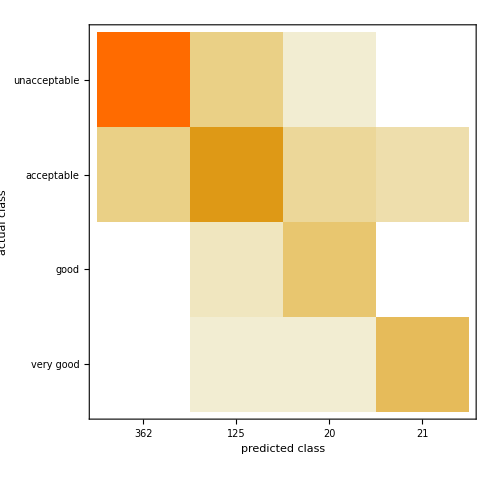

```mathematica
cm["ConfusionMatrixPlot"]
```